```mathematica
Clear[Si,s,LT,avgManualTollRate,avgElectronicTollRate]
```

```mathematica
Si=3;(*Input Lanes*)
s=9;(*Booths*)
LT=3;(*total # of lanes in a partition*)
(*Solve[s==(Si)*(LT),(*input variable to solve for*)]*)
avgManualToll=1/(350/60^2);
avgElectronicTollRate=1/(1200/60^2);
```

```mathematica
avgManualToll//N
```

```mathematica
Clear[ETCRate]
ETCRate[ETC_]:=1/avgElectronicTollRate
Clear[HRate]
HRate[H_]:=1/avgManualToll
```

```mathematica
ETCRate[3]
```

3

```mathematica
HRate[3]
```

72/7

## $$$$

```mathematica
ETCvH[3,0]
```

0.5

```mathematica
ETCvH[1,2]
```

14.8867

```mathematica
ETCvH[1,2]
```

14.8867

```mathematica
(%736+%748+%749)/3
```

1/3 (%736+%748+%749)

```mathematica
5.6/30
```

0.186667

```mathematica
Clear[ModelFunctionElectronic]
ModelFunctionElectronic[λ_,ETC_,H_]:=
QueueProperties[
QueueingProcess[
λ/(ETC+H),
ETCRate[ETC],
ETC],
"MeanSystemTime"]
```

```mathematica
Clear[ModelFunctionManual]
ModelFunctionManual[λ_,ETC_,H_]:=
QueueProperties[
QueueingProcess[
λ/(ETC+H),
HRate[H],
H],
"MeanSystemTime"]
```

```mathematica
average[ETC_,MTC_]:=(ModelFunction[10/30,ETC,MTC]+ModelFunction2[10/30,ETC,MTC])/2//N
```

```mathematica
Clear[currentSystemFunction]
currentSystemFunction[λ_,ETC_,H_]:=
{
Table[
QueueProperties[
QueueingProcess[(λ)/(ETC+H),ETCRate[ETC]
],"MeanSystemTime"],
{i,1,ETC}
],Table[
QueueProperties[
QueueingProcess[(λ)/(ETC+H),HRate[H]
],"MeanSystemTime"],{i,1,H}
]
}
```

```mathematica
Clear[avgFunction]
avgFunction[λ_,ETC_,H_]:=Total[Flatten[currentSystemFunction[ETC,H,λ]]]/(ETC+H)//N
```

Functions

```mathematica
Clear[EdgeFunction]
EdgeFunction[Si_,s_]:=Table[DirectedEdge["InitialVertex",Subscript[p, i]],{i,1,s/Si}]
```

```mathematica
EdgeFunction[Si,s]
```

{InitialVertex->p_1,InitialVertex->p_2,InitialVertex->p_3}

```mathematica
Clear[PartitionEdgeFunction]
PartitionEdgeFunction[Si_,s_,LT_]:=Flatten[Table[Map[DirectedEdge[Subscript[p, i],#]&,Partition[Map[Subscript[B, #]&,Range[s]],{LT}][[i]]],{i,1,Si}]]
```

```mathematica
PartitionEdgeFunction[Si,s,LT]
```

{p_1->B_1,p_1->B_2,p_1->B_3,p_2->B_4,p_2->B_5,p_2->B_6,p_3->B_7,p_3->B_8,p_3->B_9}

```mathematica
Flatten[{Table[PartitionEdgeFunction[Si,s,LT][[i]],{i,s,s-Si+1,-1}],Table[PartitionEdgeFunction[Si,s,LT][[i]],{i,2,Ceiling[s/2]}]}]
```

{p_3->B_9,p_3->B_8,p_3->B_7,p_1->B_2,p_1->B_3,p_2->B_4,p_2->B_5}

```mathematica
Complement[PartitionEdgeFunction[Si,s,LT],Flatten[{Table[PartitionEdgeFunction[Si,s,LT][[i]],{i,s,s-Si+1,-1}],Table[PartitionEdgeFunction[Si,s,LT][[i]],{i,2,Ceiling[s/2]}]}]]
```

{p_1->B_1,p_2->B_6}

```mathematica
Clear[MergeLaneFunction]
MergeLaneFunction[Si_,s_,LT_]:=Flatten[Table[Map[DirectedEdge[#,Subscript[m, i]]&,Partition[Map[Subscript[B, #]&,Range[s]],{LT}][[i]]],{i,1,Si}]]
```

```mathematica
Flatten[Table[Partition[MergeLaneFunction[Si,s,LT],{3}][[j,i]]->j,{i,LT,1,-1},{j,1,3}]]
```

{{B_3->m_1→1,B_6->m_2→2,B_9->m_3→3},{B_2->m_1→1,B_5->m_2→2,B_8->m_3→3},{B_1->m_1→1,B_4->m_2→2,B_7->m_3→3}}

```mathematica
Clear[EdgeFunction2]
EdgeFunction2[Si_,s_]:=Table[DirectedEdge[Subscript[m, i],"EndVertex"],{i,1,s/Si}]
```

```mathematica
EdgeFunction2[Si,s]
```

{m_1->EndVertex,m_2->EndVertex,m_3->EndVertex}

```mathematica
Clear[GraphFunction]
GraphFunction[Si_,s_,LT_,λ_,ETC_,H_]:=
Graph[
Union[
EdgeFunction[Si,s],
PartitionEdgeFunction[Si,s,LT],
MergeLaneFunction[Si,s,LT],
EdgeFunction2[Si,s]],
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Bottom},VertexStyle->
Flatten[
{Table[
PartitionEdgeFunction[
Si,s,LT][[i,2]]->Red,
{i,s,s-Si+1,-1}
],Table[
PartitionEdgeFunction[
Si,s,LT][[i,2]]->Red,
{i,2,Ceiling[s/2]}
]
}
],EdgeWeight->Flatten[
{
(*Merge Lane Edge Weights*)
Table[Partition[MergeLaneFunction[Si,s,LT],{3}][[j,i]]->i,{i,LT,1,-1},{j,2,3}],
Table[Partition[MergeLaneFunction[Si,s,LT],{3}][[1,i]]->LT-i+1,{i,1,LT}],

(*Queue Lane Edge Weights*)
Map[#->ModelFunctionManual[λ,ETC,H]&,
Complement[
PartitionEdgeFunction[Si,s,LT],
Flatten[
{Table[
PartitionEdgeFunction[Si,s,LT][[i]],{i,s,s-Si+1,-1}],
Table[
PartitionEdgeFunction[Si,s,LT][[i]],{i,2,Ceiling[s/2]
}
]
}
]
]
],
Table[
PartitionEdgeFunction[Si,s,LT][[i]]->
ModelFunctionElectronic[λ,ETC,H],
{i,s,s-Si+1,-1}
],Table[
PartitionEdgeFunction[Si,s,LT][[i]]->
ModelFunctionElectronic[λ,ETC,H],
{i,2,Ceiling[s/2]}
]

(*Initial and Ending edges*)
,Map[#->0&,Union[EdgeFunction[Si,s],EdgeFunction2[Si,s]]]}
],
EdgeLabels->"EdgeWeight"
]
```

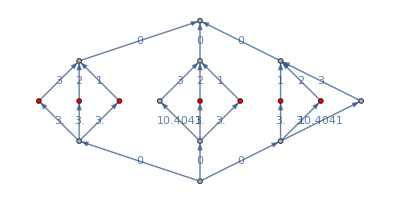

```mathematica
GraphFunction[Si,s,LT,5.6/30,7,2]
```

```mathematica
averageSystemTime[-Graphics-]
```

6.64535

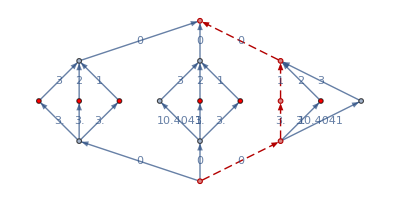

```mathematica
GraphHighlighter[-Graphics-]
```

```mathematica
Clear[currentModelEdges]
currentModelEdges[servers_]:=
Flatten[
{
Table[
DirectedEdge[
"InitialVertex",Subscript[m, i]],
{i,servers}
],
Table[
DirectedEdge[
Subscript[m, i],"EndVertex"],
{i,servers}
]
}
]
```

```mathematica
Clear[currentModelGraph]
currentModelGraph[servers_,ETC_,H_,λ_]:=
Graph[
Flatten[
{
"InitialVertex",
"EndVertex",
Table[Subscript[m, i],{i,1,servers}]
}
],
currentModelEdges[servers],
ImageSize->Large,
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Bottom},
VertexStyle->Table[Subscript[m, i]->Red,{i,servers,servers-ETC+1,-1}],EdgeWeight->Flatten[
{Table[
DirectedEdge[Subscript[m, i],"EndVertex"]->
Ceiling[servers/2]-i+1,
{i,1,Floor[servers/2]}
],
Table[
DirectedEdge[Subscript[m, i],"EndVertex"]->
i-Floor[servers/2],
{i,servers,Ceiling[servers/2],-1}
],
Table[
DirectedEdge["InitialVertex",Subscript[m, i]]->
ModelFunctionElectronic[λ,ETC,H],
{i,servers,servers-ETC+1,-1}
],
Table[
DirectedEdge["InitialVertex",Subscript[m, i]]->
ModelFunctionManual[λ,ETC,H],
{i,1,servers-ETC+1}
]
}
],
VertexLabels->"Name",
EdgeLabels->"EdgeWeight"
]
```

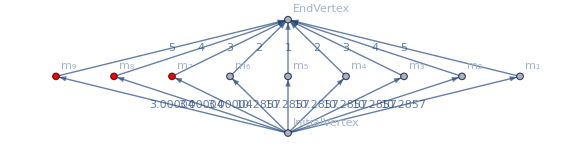

```mathematica
currentModelGraph[9,3,6,5.6/30]
```

```mathematica
Clear[GraphHighlighter]
GraphHighlighter[graph_]:=
HighlightGraph[
graph,
DirectedGraph[
PathGraph[
FindShortestPath[
graph,
"InitialVertex",
"EndVertex"
]
]
],
GraphHighlightStyle->
{"Dashed"}
]
```

```mathematica
Clear[averageSystemTime]
averageSystemTime[graph_]:=
Total[
Map[
Total[#]&,
Partition[
DeleteCases[
Flatten[
Map[
PropertyValue[
{graph,##},
EdgeWeight]&,
Map[
EdgeList[
DirectedGraph[
PathGraph[#]
]
]&,
FindPath[
graph,
"InitialVertex","EndVertex",Infinity,All]],{2}]],$Failed],{2}]]]/Length[FindPath[graph,"InitialVertex","EndVertex",Infinity,All]]
```

```mathematica
averageSystemTime[-Graphics-]
```

11.0794